```mathematica
N[theconsts]
```

{BrfpG→1.×10^15,lmode→2.,mmode→0.,rfp→rl,rl→(3. G msun)/c^2,zeta→10000.,gamma→700.,r→5.×10^13,rp→r,nu→0.75,rmono→3.×10^10,thfp→1.5708,omegaffp→(0.25 c)/rfp,gamma0→1.15}

```mathematica
pm//.theconsts//.physicalconsts
```

3.34456×10^9

```mathematica
testT=3.4*10^9
kb*testT/(me*c^2)//.physicalconsts
```

3.4×10^9

0.57337

```mathematica
urad//.theconsts//.physicalconsts//.{T->testT}
ugsimple//.theconsts//.physicalconsts//.{T->testT}
```

1.41717×10^10

9.91011×10^9

```mathematica
Qs1//.theconsts//.physicalconsts//.{T->testT}
Qs2//.theconsts//.physicalconsts//.{T->testT}
Qsnonrel//.theconsts//.physicalconsts//.{T->testT}
Qsrel//.theconsts//.physicalconsts//.{T->testT}
```

7.79364×10^7

1.83633×10^8

1.28413×10^8

1.10442×10^8

```mathematica
Rjet//.theconsts//.physicalconsts
Lp//.theconsts//.physicalconsts
```

1.09132×10^12

1.71425×10^12

```mathematica
tausca//.theconsts//.physicalconsts
tauabs//.theconsts//.physicalconsts//.{T->testT}
tautot//.theconsts//.physicalconsts//.{T->testT}
```

0.25864

1.03855×10^-14

0.25864

```mathematica
gtau//.theconsts//.physicalconsts//.{T->testT}
htau//.theconsts//.physicalconsts//.{T->testT}
urad//.theconsts//.physicalconsts//.{T->testT}
prad//.theconsts//.physicalconsts//.{T->testT}
```

2.20173×10^-14

1.03855×10^-14

2.22609×10^10

7.4203×10^9

```mathematica
(kb*testT)/(me*c^2)//.physicalconsts
(kb*8*10^8)/(me*c^2)//.physicalconsts
(kb*4.2*10^9)/(me*c^2)//.physicalconsts
```

0.57337

0.134911

0.70828

```mathematica
prad//.theconsts//.physicalconsts//.{T->testT}
ppairs//.theconsts//.physicalconsts//.{T->testT}
pe//.theconsts//.physicalconsts//.{T->testT}
pb//.theconsts//.physicalconsts//.{T->testT}
```

7.4203×10^9

2.26995×10^9

334553.

334553.

```mathematica
pg//.theconsts//.physicalconsts//.{T->testT}
pgbalance//.theconsts//.physicalconsts//.{T->testT}
```

9.69092×10^9

3.30337×10^9

```mathematica
npairs//.theconsts//.physicalconsts//.{T->testT}
ne//.theconsts//.physicalconsts//.{T->testT}
```

9.23535×10^15

3.56345×10^11

```mathematica
Exp[-(me*c^2)/(kb*T)]//.theconsts//.physicalconsts//.{T->testT}
```

0.174807

```mathematica
rhob//.theconsts//.physicalconsts
(rhob/mb)//.theconsts//.physicalconsts
ne//.theconsts//.physicalconsts
```

1.18345×10^-12

7.1269×10^11

3.56345×10^11

```mathematica
(* **************** *)
```

```mathematica
mypg=pg//.theconsts//.physicalconsts;
myprad=prad//.theconsts//.physicalconsts;
myppairs=ppairs//.theconsts//.physicalconsts;
mypb=pb//.theconsts//.physicalconsts;
mype=pe//.theconsts//.physicalconsts;
mypgsimple=pgsimple//.theconsts//.physicalconsts;
mypm=pm//.theconsts//.physicalconsts;
```

```mathematica
jsynch//.theconsts//.physicalconsts//.{T->testT}
jsynchrel//.theconsts//.physicalconsts//.{T->testT}
jsynchnonrel//.theconsts//.physicalconsts//.{T->testT}
```

0.000515325

0.00030993

0.00036036

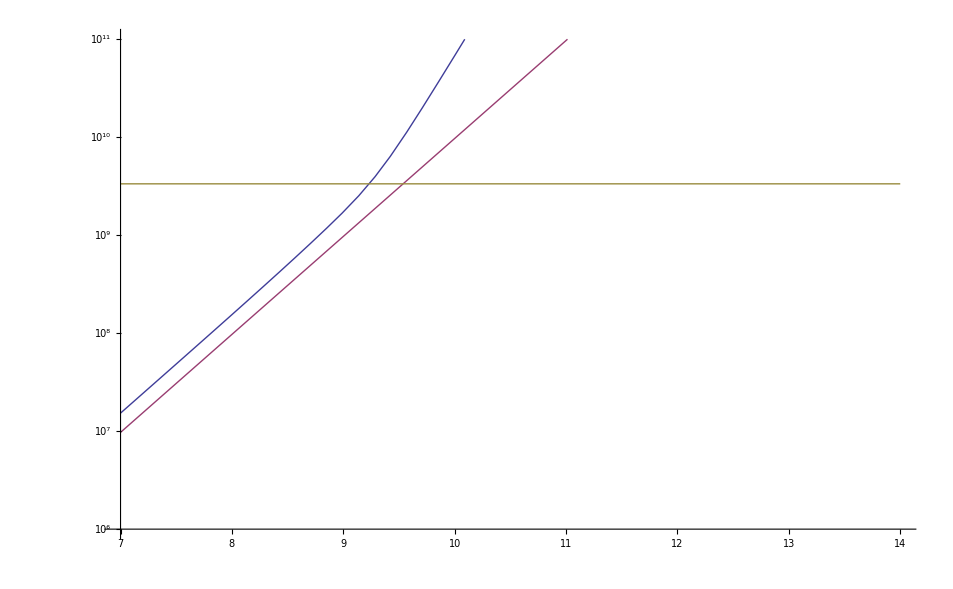

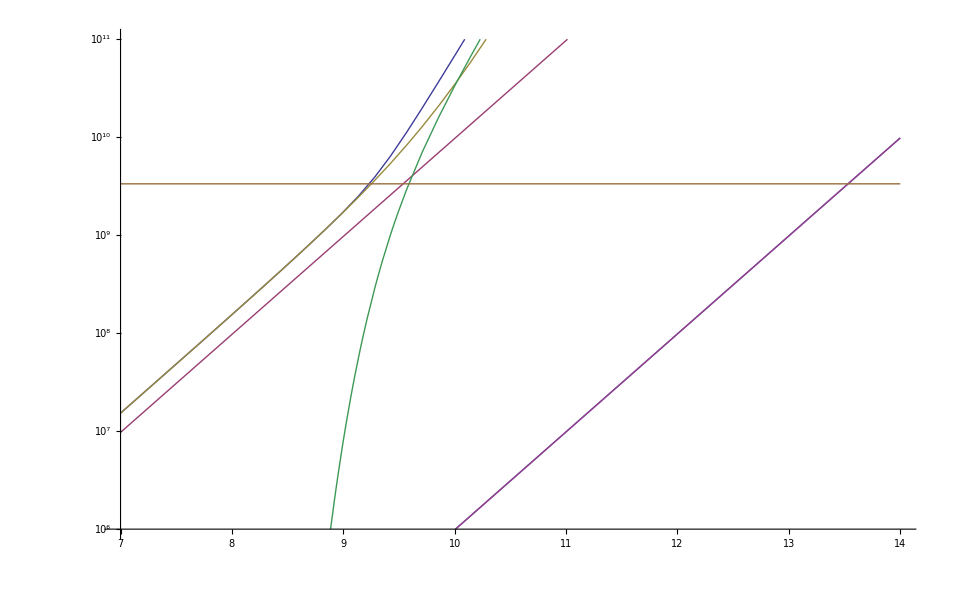

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{T→2.33487×10^9}

{T→3.44239×10^9}

{T→1.78741×10^9}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{T→3.87752×10^9}

{T→3.399×10^13}

{T→3.399×10^13}

```mathematica
plotpg=mypg//.{T->10^lT};
plotprad=myprad//.{T->10^lT};
plotppairs=myppairs//.{T->10^lT};
plotpb=mypb//.{T->10^lT};
plotpe=mype//.{T->10^lT};
plotpgsimple=mypgsimple//.{T->10^lT};
LogPlot[{plotpg,plotpgsimple,mypm},{lT,7,14},PlotRange->{10^6,10^(11)}]
LogPlot[{plotpg,plotpgsimple,plotprad,plotppairs,plotpb,plotpe,mypm},{lT,7,14},PlotRange->{10^6,10^(11)}]
(* find crossing *)
mypg=pg//.theconsts//.physicalconsts;
mypgsimple=pgsimple//.theconsts//.physicalconsts;
mypm=pm//.theconsts//.physicalconsts;
FindRoot[mypg==mypm,{T,10^(10)}]
FindRoot[mypgsimple==mypm,{T,10^(10)}]
FindRoot[myprad==mypm,{T,10^(10)}]
FindRoot[myppairs==mypm,{T,10^(10)}]
FindRoot[mypb==mypm,{T,10^(10)}]
FindRoot[mype==mypm,{T,10^(10)}]
```

```mathematica
eq=pgsimple-pm==0;
solsT=Solve[eq,T]
mysolsT1=solsT[[1]];
mysolsT2=solsT[[2]];
myT=mysolsT1[[1,2]]
```

{{T→-((rmono/rfp)^-nu Csc[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]] (4 √3 BrfpG^2 c^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb me rfp^2 (rmono/rfp)^nu sigmat Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]-√(576 √3 BrfpG^2 c^6 gamma gamma0 √((-1+gamma0^2)/gamma0^2) kb^2 mb me^2 π r rfp^2 (rmono/rfp)^nu sigmat zeta Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]+48 BrfpG^4 c^4 (-1+gamma0^2) kb^2 me^2 rfp^4 (rmono/rfp)^(2 nu) sigmat^2 Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)))/(6 √3 BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb^2 rfp^2 sigmat)},{T→-((rmono/rfp)^-nu Csc[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]] (4 √3 BrfpG^2 c^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb me rfp^2 (rmono/rfp)^nu sigmat Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]+√(576 √3 BrfpG^2 c^6 gamma gamma0 √((-1+gamma0^2)/gamma0^2) kb^2 mb me^2 π r rfp^2 (rmono/rfp)^nu sigmat zeta Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]+48 BrfpG^4 c^4 (-1+gamma0^2) kb^2 me^2 rfp^4 (rmono/rfp)^(2 nu) sigmat^2 Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)))/(6 √3 BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb^2 rfp^2 sigmat)}}

-((rmono/rfp)^-nu Csc[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]] (4 √3 BrfpG^2 c^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb me rfp^2 (rmono/rfp)^nu sigmat Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]-√(576 √3 BrfpG^2 c^6 gamma gamma0 √((-1+gamma0^2)/gamma0^2) kb^2 mb me^2 π r rfp^2 (rmono/rfp)^nu sigmat zeta Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]+48 BrfpG^4 c^4 (-1+gamma0^2) kb^2 me^2 rfp^4 (rmono/rfp)^(2 nu) sigmat^2 Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]]^2)))/(6 √3 BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb^2 rfp^2 sigmat)

```mathematica
solsT//.theconsts//.physicalconsts
```

{{T→1.81063×10^10},{T→-2.60128×10^10}}

```mathematica
Aum//.mysolsT//.theconsts//.physicalconsts
```

1.36035

```mathematica
othertheconsts={BrfpG->1000000000000000,lmode->2,mmode->0,rfp->rl,rl->(3 G msun)/c^2,zeta->10000,gamma->700,r->10^(15),rp->r,nu->3/4,rmono->30000000000,thfp->π/2,omegaffp->(0.25 c)/rfp,gamma0->1.15};
```

```mathematica
conditionpt//.mysolsT//.theconsts//.physicalconsts
conditionpt//.mysolsT//.othertheconsts//.physicalconsts
```

0.594201

1.10652

```mathematica
finalconditionpt=conditionpt//.mysolsT;
```

```mathematica
Print["fullsimpl"];
god=Simplify[finalconditionpt,{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0}];
Print["powerexpand"];
god2=PowerExpand[god];
Print["solving"];
solsrat=Solve[god2==1,r];
```

fullsimpl

$Aborted

powerexpand

solving

```mathematica
Series[finalconditionpt,{r,Infinity,0}]
```

$Aborted

```mathematica
.
```

```mathematica
test=finalconditionpt//.{BrfpG->1000000000000000,lmode->2,mmode->0,rfp->rl,rl->(3 G msun)/c^2,zeta->10000,gamma->700,rp->r,nu->3/4,rmono->30000000000,thfp->π/2,omegaffp->(0.25 c)/rfp,gamma0->1.15}//.physicalconsts;
```

```mathematica
Series[PowerExpand[Simplify[test,{r>0}]],{r,10^(15),1}]
```

1.10652+5.62824×10^-16 (r-1000000000000000)+O[r-1000000000000000]^2

```mathematica
test=finalconditionpt;
Series[test,{r,10^4*rmono,0}]
```

$Aborted

```mathematica
pgsimple
```

(BrfpG^4 √(1-1/gamma0^2) gamma0 omegaffp^2 rfp^2 rmono^4 (rmono/rfp)^(-4+2 nu) sigmat Sin[thfp/2]^2 Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]])/(24 √3 c^4 gamma^3 mb π^2 r^3 (1-(3 kb T (2+(3 kb T)/(2 c^2 me)))/(2 c^2 me (1+(3 kb T)/(2 c^2 me))^2)) zeta)

```mathematica
Qs
```

(3 BrfpG^4 √(1-1/gamma0^2) gamma0 kb^2 omegaffp^2 rfp^2 rmono^4 (rmono/rfp)^(-4+2 nu) sigmat T^2 Sin[thfp/2]^2)/(16 c^7 gamma^3 mb me^2 π^2 r^4 zeta)

```mathematica
me*c^2/kb//.physicalconsts
```

5.92986×10^9

```mathematica
pgbalance
```

(BrfpG^4 √(1-1/gamma0^2) gamma0 kb omegaffp^2 q^4 rfp^2 rmono^4 (rmono/rfp)^(-4+2 nu) T Sin[thfp/2]^2 Sin[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]])/(4 √3 c^10 gamma^3 mb me^3 r^3 zeta)

```mathematica
eq=pgbalance-pm==0;
solsT=Solve[eq,T]
```

{{T→(2 √3 c^8 gamma mb me^3 r (rmono/rfp)^-nu zeta Csc[2 (rmono/rfp)^(-nu/2) Sin[thfp/2]])/(BrfpG^2 gamma0 √((-1+gamma0^2)/gamma0^2) kb π q^4 rfp^2)}}

```mathematica
(**************)
```

3.34456×10^9

0.229145 10^lT (2 √3+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 10^lnpairs))

8.71331×10^15 (2 √3+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 10^lnpairs)) ⅇ^(-5.92986×10^9 10^-lT)

3.56345×10^11

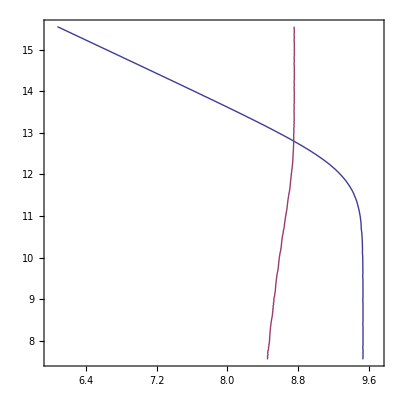

FindRoot::precw: The precision of the argument function ({0.22914485128808626` 10^lT (2 √3 + 1.9952319114906517`*^-24 (3.8888748759523905`*^23 + 1.714247046101083`*^12 Power[« 2 »])) == 3.344555004005957`*^9, 8.713312560115926`*^15 (2 √3 + 1.9952319114906517`*^-24 (3.8888748759523905`*^23 + 1.714247046101083`*^12 Power[« 2 »])) ⅇ^-5.929856910549337`*^9 10^-lT == 10^lnpairs}) is less than WorkingPrecision (30.).

{lT→8.75260520344839385543075458946,lnpairs→12.7995854991758118189253956753}

```mathematica
pmtouse=pm//.theconsts//.physicalconsts
pgtouse=pgbalance//.theconsts//.physicalconsts//.{T->10^lT,npairs->10^lnpairs}
npairstouse=npairsfuncbalance//.theconsts//.physicalconsts//.{T->10^lT,npairs->10^lnpairs}
netouse=ne//.theconsts//.physicalconsts//.{T->10^lT,npairs->10^lnpairs}
ContourPlot[{pgtouse==pmtouse,npairstouse==10^lnpairs},{lT,6,Log[10,5*10^9]},{lnpairs,Log[10,0.0001*netouse],Log[10,10000*netouse]}]
FindRoot[{pgtouse==pmtouse,npairstouse==10^lnpairs},{lT,8},{lnpairs,Log[10,2*netouse]},WorkingPrecision->30]
```

```mathematica
npairstouse//.{lT->8.7,lnpairs->12.76}
```

1.76171×10^16

```mathematica
godT=10^(8.7)
kb*godT//.physicalconsts
1-Exp[-kb*godT/(me*c^2)]//.physicalconsts
kb*godT/(me*c^2)//.physicalconsts
Exp[-me*c^2/(kb*godT)]//.physicalconsts
Normal[Series[Exp[-1/x],{x,1,40}]]//.{x->kb*godT/(me*c^2)}//.physicalconsts
```

5.01187×10^8

6.91968×10^-8

0.0810461

0.0845193

7.27098×10^-6

0.00127608

```mathematica
Normal[Series[Exp[-1/x],{x,1,1}]]
```

1/ⅇ+(x-1)/ⅇ+O[x-1]^2

```mathematica
Series[1-Exp[-x],{x,0,1}]
```

x+O[x]^2

3.34456×10^9

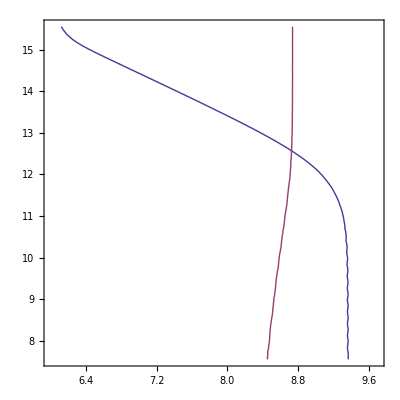

FindRoot::precw: The precision of the argument function ({0.00019679612478892662` 10^lT + 2.5219781934011094`*^-15 10^4 lT (2 √3 + 3 (Times[« 2 »] + Times[« 5 »]))/2 Power[« 2 »] + 6.076616062864569`*^-12 Power[« 2 »] Plus[« 2 »] Power[« 2 »] Power[« 2 »] + 3 Plus[« 2 »] + 4.413461838451941`*^-15 10^4 lT (2 √3 + 3 (Times[« 2 »] + Times[« 5 »])) ⅇ^-5.929856910549337`*^9 10^Times[« 2 »]/2 Power[« 2 »] + 6.076616062864569`*^-12 Power[« 2 »] Plus[« 2 »] Power[« 2 »] Power[« 2 »] + 3 Plus[« 2 »] == 3.344555004005957`*^9, 95.89909677382686` « 2 » « 1 »/2 √3 + « 1 » + 3 (Times[« 1 »] + « 1 ») == « 1 »}) is less than WorkingPrecision (30.).

{lT→8.7285953211894381732742342327,lnpairs→12.5648146372381342734819016586}

```mathematica
pmtouse=pm//.theconsts//.physicalconsts
pgtouse=pg//.theconsts//.physicalconsts//.{T->10^lT,npairs->10^lnpairs};
npairstouse=npairsfunc//.theconsts//.physicalconsts//.{T->10^lT,npairs->10^lnpairs};
netouse=ne//.theconsts//.physicalconsts//.{T->10^lT,npairs->10^lnpairs};
ContourPlot[{pgtouse==pmtouse,npairstouse==10^lnpairs},{lT,6,Log[10,5*10^9]},{lnpairs,Log[10,0.0001*netouse],Log[10,10000*netouse]}]
FindRoot[{pgtouse==pmtouse,npairstouse==10^lnpairs},{lT,8},{lnpairs,Log[10,2*netouse]},WorkingPrecision->30]
```

```mathematica
fuck1=npairsfuncbalance//.theconsts//.physicalconsts
fuck2=pgbalance//.theconsts//.physicalconsts
```

8.71331×10^15 ⅇ^(-5.92986×10^9/T) (2 √3+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 npairs))

0.229145 (2 √3+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 npairs)) T

```mathematica
1.9952319114906517*^-24 (3.8888748759523905*^23+1.714247046101083*^12 npairs)//.{npairs->10^lnpairs,T->10^lT}//.{lT->8.75260520344839385543075458945937211058`30.,lnpairs->12.79958549917581181892539567525805668217`30.}
```

22.3361

```mathematica
Solve[{fuck1==npairs,fuck2==pmtouse},{T,npairs}]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[{8.71331×10^15 ⅇ^(-5.92986×10^9/T) (2 √3+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 npairs))==npairs,0.229145 (2 √3+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 npairs)) T==3.34456×10^9},{T,npairs}]

```mathematica
Solve[fuck2==pmtouse,T]
```

{{T→(1.45958×10^10)/(3.4641+1.99523×10^-24 (3.88887×10^23+1.71425×10^12 npairs))}}

```mathematica
solsT
```

{{T→(12 c^8 gamma mb me^3 r^2 (rmono/rfp)^(2-nu) (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) zeta)/(BrfpG^2 √(1-1/gamma0^2) gamma0 kb π q^4 rmono^2 (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))}}

```mathematica
the
```

```mathematica
solsT
```

{{T→(12 c^8 gamma mb me^3 r^2 (rmono/rfp)^(2-nu) (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) zeta)/(BrfpG^2 √(1-1/gamma0^2) gamma0 kb π q^4 rmono^2 (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))}}

```mathematica
eq
```

-(BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(2 c^2 gamma^2 π r^2)+(BrfpG^4 √(1-1/gamma0^2) gamma0 kb omegaffp^2 q^4 rfp^2 rmono^4 (rmono/rfp)^(-4+2 nu) T Sin[thfp/2]^2 (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))/(24 c^10 gamma^3 mb me^3 r^4 (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) zeta)==0

```mathematica
FullSimplify[PowerExpand[myT]]
```

$Aborted

```mathematica
eq
```

-(BrfpG^2 omegaffp^2 rfp^2 rmono^2 (rmono/rfp)^(-2+nu) Sin[thfp/2]^2)/(2 c^2 gamma^2 π r^2)+(BrfpG^4 √(1-1/gamma0^2) gamma0 kb omegaffp^2 q^4 rfp^2 rmono^4 (rmono/rfp)^(-4+2 nu) T Sin[thfp/2]^2 (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))/(24 c^10 gamma^3 mb me^3 r^4 (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) zeta)==0

```mathematica
Aum//.
```

```mathematica
theconsts
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,r→50000000000000,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15}

```mathematica
godconsts={BrfpG->1000000000000000,lmode->2,mmode->0,rfp->rl,rl->(3 G msun)/c^2,zeta->10000,gamma->700,rp->r,nu->3/4,rmono->30000000000,thfp->π/2,omegaffp->(0.25 c)/rfp,gamma0->1.15}
```

{BrfpG→1000000000000000,lmode→2,mmode→0,rfp→rl,rl→(3 G msun)/c^2,zeta→10000,gamma→700,rp→r,nu→3/4,rmono→30000000000,thfp→π/2,omegaffp→(0.25 c)/rfp,gamma0→1.15}

```mathematica
conditionpt//.solsT//.godconsts//.physicalconsts
```

{(8.19106×10^-9)/(√Lp √(1/r^2))}

```mathematica
solsT
```

{{T→(12 c^8 gamma mb me^3 r^2 (rmono/rfp)^(2-nu) (npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu))/(16 c^2 gamma mb π r^2 zeta)) zeta)/(BrfpG^2 √(1-1/gamma0^2) gamma0 kb π q^4 rmono^2 (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta)) (2 √3+3 sigmat (lmode Lp npairs+(BrfpG^2 √(1-1/gamma0^2) gamma0 rmono^2 (rmono/rfp)^(-2+nu/2) Sin[thfp/2])/(8 c^2 gamma mb π r zeta))))}}

```mathematica
conditionpt//.solsT
```

{(c √(π/2))/(√((BrfpG^2 √(1-1/gamma0^2) gamma0 q^2 rmono^2 (rmono/rfp)^(-2+nu))/(c^2 gamma mb^2 r^2 zeta)) √((Lp mb omegaffp^2 rfp^2 sigmat zeta Sin[thfp/2]^2)/(gamma √(1-1/gamma0^2) gamma0 q^2)))}

```mathematica
rat=conditionpt//.solsT;
rat=FullSimplify[rat,{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0,gamma0>1,q>0,rmono>rfp,kb>0,omegaffp>0,sigmat>0,thfp>0,thfp≤Pi/2,npairs>0,lmode>0,mu>0,mu<2,gamma>1,c>0,me>0}]
```

{(c^2 gamma √(π/2) r Csc[thfp/2])/(BrfpG √(Lp mb) omegaffp rfp √((rfp^(2-nu) rmono^nu sigmat)/mb^2))}

```mathematica
(*myrat=solsrat[[5,1,2]]*)
myrat=FullSimplify[solsrat[[1,1,2]],{BrfpG>0,zeta>0,r>0,rfp>0,Lp>0,thetajet>0,gamma>0,Lp>0}]
PowerExpand[myrat]
PowerExpand[%//.{gamma0->mygamma0,omegaffp->myomegaffp}//.simpleconsts//.physicalconsts]
```